## Import Data

```mathematica
dat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\test_set_WB.xlsx"];
```

```mathematica
dat//First//Keys//Normal
```

{reaction number,page number,reaction class,true reaction smiles,notes}

```mathematica
rxnClasses=Normal[DeleteDuplicates@dat[All,"reaction class"]]
```

{substitution,elimination,grignard,organocopper,friedelcrafts,dielsalder,acetylide,esub,carbonylcondensation,amine}

## IBM Rxn API Wrapper Code - (https://github.com/wrborrelli/IBMRxnAPI)

### Necessary Variable Assignments

```mathematica
(* Initial run of this notebook will prompt you to enter your authorization key. Once you've done that feel free to delete the following cell. *)
```

```mathematica
(*SystemCredential["authKey"]=InputString["Authorization Key"];*)
```

```mathematica
authKey=SystemCredential["authKey"];
```

### Wrapper Code

```mathematica
baseURL="rxn.res.ibm.com";
```

```mathematica
IBMRxn[req_String,molecs_List,projID_String]:=Module[
{reactantList={},createProj,projectID,createPred,getPred,rxnImg,rxnConf,predID,projName,reactants},

If[(* If[] you want to make a "new prediction", this code block runs *)
req=="new prediction",
Do[
Which[
ImageQ[molecs[[i]]],
AppendTo[reactantList,MoleculeRecognize[molecs[[i]]]["SMILES"]]
,
StringQ[molecs[[i]]],
AppendTo[reactantList,molecs[[i]]]
],{i,1,Length[molecs]}];

reactants=ToString[Row[#,"."]&@reactantList];
createPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/pr?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
predID=createPred["payload","id"];

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projectID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
]]
```

```mathematica
(* duplicate of above - for adding a output format parameter *)
```

```mathematica
IBMRxn[req_String,molecs_List,projID_String,outType_String]:=Module[
{reactantList={},createProj,projectID,createPred,getPred,rxnImg,rxnConf,predID,projName,reactants,rsmiles},

If[(* If[] you want to make a "new prediction", this code block runs *)
req=="new prediction",
Do[
Which[
ImageQ[molecs[[i]]],
AppendTo[reactantList,MoleculeRecognize[molecs[[i]]]["SMILES"]]
,
StringQ[molecs[[i]]],
AppendTo[reactantList,molecs[[i]]]
],{i,1,Length[molecs]}];

reactants=ToString[Row[#,"."]&@reactantList];
createPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/pr?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
predID=createPred["payload","id"];

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

Which[
outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projectID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];
rsmiles=getPred["payload","attempts"][[1]]["smiles"];

<|"project name"->projName,"projID"->projectID,"predID"->predID,"rreac"->reacSplit[rsmiles][[1]],"rprod"->reacSplit[rsmiles][[2]],"conf"->rxnConf,"reaction image"->rxnImg|>//Dataset
]
]]
```

```mathematica
(* for getting more outcomes from a prediction that you've already made *)
```

```mathematica
IBMRxn[req_String,projID_String,predID_String]:=Module[
{getPred,reactants,morePreds,projName,rxnImgList={},rxnConfList={},rxnImages,rxnTables,preds},

If[req=="more predictions",
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
reactants=getPred["payload","request","reactants"];

Pause[10];

morePreds=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/prb?predictionId="<>predID<>"&projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];


rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;
rxnTables=TableForm[{{projName,projID,predID,#}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]&/@rxnConfList;

preds=Partition[Riffle[rxnImages,rxnTables],2];
preds
]]
```

```mathematica
(* duplicate of above - for adding an output type *)
```

```mathematica
IBMRxn[req_String,projID_String,predID_String,outType_String]:=Module[
{getPred,reactants,morePreds,projName,rxnImgList={},rxnConfList={},rsmilesList={},rxnImages,rxnTables,preds},

If[req=="more predictions",
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
reactants=getPred["payload","request","reactants"];

Pause[10];

morePreds=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/prb?predictionId="<>predID<>"&projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

Which[
outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];


rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;
rxnTables=TableForm[{{projName,projID,predID,#}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]&/@rxnConfList;

preds=Partition[Riffle[rxnImages,rxnTables],2];
preds
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
	Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each rsmiles to the list *)
AppendTo[rsmilesList,getPred["payload","attempts"][[i]]["smiles"]],
{i,1,Length[getPred["payload","attempts"]]}];

rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;

Dataset@MapThread[<|"project name"->projName,"projID"->projID,"predID"->predID,"rreac"->reacSplit[#1][[1]],"rprod"->reacSplit[#1][[2]],"conf"->#2,"reaction image"->#3|>&,{rsmilesList,rxnConfList,rxnImages}]
]
]]
```

```mathematica
(* for making a new retrosynthesis *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100]},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->"",
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];

retImg
retTable
]]
```

```mathematica
(* duplicate of above - added to specify a precursor *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List,prec_String]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],out,seqs,childsNumb,cImgs,childs,product},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->prec,
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];*)

seqs=Length@getRet["payload","sequences"];

retImg=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{product,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]

(*retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];*)
]]
```

```mathematica
(* duplicate of above - added to specify output type *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List,prec_String,outType_String]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],out,seqs,childsNumb,cImgs,childs,product,cols,cSMILES,retroID},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->prec,
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];*)

Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

retImg=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{product,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

cols=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"];
retroID=getRet["payload","sequences"][[1]]["retrosynthesisId"];
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cSMILES=Flatten@Rest@out;

{rClass,projID,retroID,cSMILES,product,retConf,retOptScore}
,{i,1,seqs}];
MapThread[<|"rclass"->#1,"projID"->#2,"retroID"->#3,"rreac"->StringRiffle[#4,"."],"prod"->#5,"conf"->#6,"opt"->#7|>&,{cols[[All,1]],cols[[All,2]],cols[[All,3]],cols[[All,4]],cols[[All,5]],cols[[All,6]],cols[[All,7]]}]//Dataset
]

(*retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];*)
]]
```

```mathematica
(* for making a new project, listing all project attempts, or recovering a past prediction or retrosynthesis *)
```

```mathematica
IBMRxn[req_String,IDorName_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,allProjAs,getPred,projName,rxnImg,rxnConf,predID,projID,createProj,projectID,getRet,seqMolecList,seqSMILES,retConf,retOptScore,molecPlots,retTable,stepsImgs,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],stepDescs,retImg,prodSMILES,rClass,seqConf,seqs,prod,childsNumb,out,cImgs,childs},

Which[
req=="new project",(* for a "new project", following code block runs *)
createProj=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"name"->ToString[IDorName],"invitations"->{}|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
projectID=createProj["payload","id"];
TableForm[{{IDorName,projectID}},TableHeadings->{None,{"Project Name","Project ID"}}]
,
req== "all project attempts",(* for getting "all project attempts", following code block runs *)
allProjAs=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects/"<>IDorName<>"/attempts?raw={}"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
allProjAs,
req=="recover prediction",(* to "recover prediction", following code block runs *)
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
req=="recover retrosynthesis",(* recover a previously made retrosynthesis *)
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

While[
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
projID=getRet["payload","projectId"];

(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

prodSMILES=getRet["payload","wizardParameters","exclude_smiles"][[1]];
molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];

retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)

seqs=Length@getRet["payload","sequences"];

retImg=Table[
prod=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{prod,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,IDorName,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]

(*retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)
]]
```

```mathematica
(* duplicate of above - added to allow for specifying ouput type *)
```

```mathematica
IBMRxn[req_String,IDorName_String,outType_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,allProjAs,getPred,projName,rxnImg,rxnConf,predID,projID,createProj,projectID,getRet,seqMolecList,seqSMILES,retConf,retOptScore,molecPlots,retTable,stepsImgs,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],stepDescs,retImg,prodSMILES,rClass,seqConf,seqs,prod,childsNumb,out,cImgs,childs,retroID,product,cols,cSMILES,rsmiles},

Which[
req=="new project",(* for a "new project", following code block runs *)
createProj=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"name"->ToString[IDorName],"invitations"->{}|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
projectID=createProj["payload","id"];
TableForm[{{IDorName,projectID}},TableHeadings->{None,{"Project Name","Project ID"}}]
,
req== "all project attempts",(* for getting "all project attempts", following code block runs *)
allProjAs=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects/"<>IDorName<>"/attempts?raw={}"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
allProjAs,
req=="recover prediction",(* to "recover prediction", following code block runs *)
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];
rsmiles=getPred["payload","attempts"][[1]]["smiles"];

<|"project name"->projName,"projID"->projID,"predID"->predID,"rreac"->reacSplit[rsmiles][[1]],"rprod"->reacSplit[rsmiles][[2]],"conf"->rxnConf,"reaction image"->rxnImg|>//Dataset
]
,
req=="recover retrosynthesis",(* recover a previously made retrosynthesis *)
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

While[
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
projID=getRet["payload","projectId"];

(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

prodSMILES=getRet["payload","wizardParameters","exclude_smiles"][[1]];
molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];

retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)

Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

retImg=Table[
prod=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{prod,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,IDorName,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

cols=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"];
retroID=getRet["payload","sequences"][[1]]["retrosynthesisId"];
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cSMILES=Flatten@Rest@out;

{rClass,projID,retroID,cSMILES,product,retConf,retOptScore}
,{i,1,seqs}];
MapThread[<|"rclass"->#1,"projID"->#2,"retroID"->#3,"rreac"->StringRiffle[#4,"."],"prod"->#5,"conf"->#6,"opt"->#7|>&,{cols[[All,1]],cols[[All,2]],cols[[All,3]],cols[[All,4]],cols[[All,5]],cols[[All,6]],cols[[All,7]]}]//Dataset
]

(*retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)
]]
```

```mathematica
(* just for getting all stored projects. if "stored projects" is given as input, outputs a dataset of all stored projects as well as the total number of projects stored *)
```

```mathematica
IBMRxn[req_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,queueState},
Which[(* If[] you want to get all "stored projects", this code block runs *)
req=="stored projects",
myProjects=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;

myProjNames=#["name"]&/@myProjects["payload","content"];
myProjIDs=#["id"]&/@myProjects["payload","content"];

nameRule=("Project Name"->#&/@myProjNames);
idRule=("Project ID"->#&/@myProjIDs);

myProjectsData=
Dataset[
Association[#]&/@Transpose[{nameRule,idRule}]]
TableForm[{{ToString[myProjects["payload","totalElements"]]}},TableHeadings->{None,{"Total Stored Projects"}},TableAlignments->Center]
,
req=="queue status",(* get the status of the retrosynthesis queue *)
queueState=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/queue-state"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;

queueState
]]
```

## Helper Functions

```mathematica
(* get predictions for all reactions *)
```

```mathematica
mapRets[reacsList_,projID_]:=Dataset[Flatten@Normal@ResourceFunction["MapBatched"][IBMRxn["new prediction",#,projID,"dataset"]&,reacsList,Pause[10],1]]
```

```mathematica
(* needed for rxn wrapper - splits reaction strings into reactants and products *)
```

```mathematica
reacSplit[reacs_String]:=StringSplit[reacs,">>"];
```

```mathematica
(* plots a given reaction string *)
```

```mathematica
rxnPlt[rsmiles_String,title_String,rclass_String]:=Module[{plus=Graphics[Text@Style["+",20],BaselinePosition->Center,ImageSize->100],arrow=Graphics[Text@Style["→",20],BaselinePosition->Center,ImageSize->100],reacsplit,reacs,prods,reacPlots,prodPlots},
reacsplit=reacSplit[rsmiles];
reacs=StringSplit[reacsplit[[1]],"."];
prods=StringSplit[reacsplit[[2]],"."];
reacPlots=Table[MoleculePlot[Molecule[i],ImageSize->Large],{i,reacs}];
prodPlots=Table[MoleculePlot[Molecule[j],ImageSize->Large],{j,prods}];
Show[GraphicsRow[Flatten[{Riffle[reacPlots,plus],arrow,Riffle[prodPlots,plus]}],ImageSize->Full,Frame->True],PlotLabel->title<>"\n"<>rclass,LabelStyle->{FontFamily->"Cambria",12,GrayLevel[0]}]
]
```

```mathematica
(* test if the molecules are the same with or without stereochemistry *)
```

```mathematica
sameProd[trProd_,prProd_]:=Module[{tprodSt,pprodSt,tprod,pprod},
Which[
Not[StringContainsQ[trProd,"."]],
tprodSt=Molecule[trProd];
pprodSt=Molecule[prProd];
tprod=MoleculeModify[tprodSt,"RemoveStereochemistry"];
pprod=MoleculeModify[pprodSt,"RemoveStereochemistry"];
MoleculeEquivalentQ[tprodSt,pprodSt]||MoleculeEquivalentQ[tprod,pprod]||MoleculeEquivalentQ[tprodSt,pprod]||MoleculeEquivalentQ[tprod,pprodSt]
,
StringContainsQ[trProd,"."],
tprodSt=Map[Molecule[#]&,StringSplit[trProd,"."]];
pprodSt=Molecule[prProd];
tprod=Map[MoleculeModify[#,"RemoveStereochemistry"]&,tprodSt];
pprod=MoleculeModify[pprodSt,"RemoveStereochemistry"];
MemberQ[Map[MoleculeEquivalentQ[#,pprodSt]&,tprodSt],True]||MemberQ[Map[MoleculeEquivalentQ[#,pprod]&,tprod],True]||MemberQ[Map[MoleculeEquivalentQ[#,pprod]&,tprodSt],True]||MemberQ[Map[MoleculeEquivalentQ[#,pprodSt]&,tprod],True]
]]
```

```mathematica
(* check if the predicted product matches the true product *)
```

```mathematica
predProdMatches[dat_,rClass_String]:=Quiet[MapThread[sameProd[#1,#2]&,{Normal[Values@dat[Select[#"true rclass"==rClass&]][All,{"true prod","pred prod"}]][[All,1]],Normal[Values@dat[Select[#"true rclass"==rClass&]][All,{"true prod","pred prod"}]][[All,2]]}]]
```

```mathematica
(* same as above but adds a feature for multiple reactions and taking top k predictions *)
```

```mathematica
predProdMatches[dat_Dataset,rClass_String,k_Integer]:=Module[{maxRNumb,minRNumb,reacs,reacIt},
maxRNumb=Round[Max[Normal[dat[Select[#"true rclass"==rClass&]][All,{"reaction number","true prod","pred prod"}][All,"reaction number"]]],1];
minRNumb=Round[Min[Normal[dat[Select[#"true rclass"==rClass&]][All,{"reaction number","true prod","pred prod"}][All,"reaction number"]]],1];
reacs=Take[#,UpTo[k]]&/@Table[dat[Select[#"true rclass"==rClass&]][All,{"reaction number","true prod","pred prod"}][Select[IntegerPart[#"reaction number"]==i&]],{i,Range[minRNumb,maxRNumb]}];
Map[(reacIt=#;
If[Length[reacIt]==1,
Quiet[sameProd[First[reacIt]["true prod"],First[reacIt]["pred prod"]]]
,
MemberQ[Quiet[MapThread[sameProd[#1,#2]&,{Normal[reacIt[All,"true prod"]],Normal[reacIt[All,"pred prod"]]}]],True]
])&,reacs]
]
```

```mathematica
(* get the additional predictions and reformat the dataset (this dataset includes the initial prediction and subsequent) *)
```

```mathematica
morePreds[dat_]:=Module[{rnumb=dat["reaction number"],trclass=dat["true rclass"],trsmiles=dat["true reaction smiles"],tprod=dat["true prod"],predrsmiles=dat["pred reaction smiles"],predprod=dat["pred prod"],conf=dat["conf"],projID=dat["projID"],predID=dat["predID"],predProdSame=dat["pred prod same"],morePreds,numbAdded,totalReacs,reacNumbs,rclassList,trsmilesList,tprodList,rsmilesList,confList,projIDList,predIDList,rprodList},
morePreds=IBMRxn["more predictions",projID,predID,"dataset"];
numbAdded=Length[morePreds];
totalReacs=numbAdded;
reacNumbs=Prepend[Range[rnumb+0.2,(rnumb+0.1)+((totalReacs-1)*0.1),0.1],rnumb];
rclassList=Table[trclass,totalReacs];
trsmilesList=Table[trsmiles,totalReacs];
tprodList=Table[tprod,totalReacs];
If[numbAdded>1,
rsmilesList=Map[StringRiffle[#,">>"]&,Values[Normal[morePreds[All,{"rreac","rprod"}]]]];
rprodList=Normal[morePreds[All,"rprod"]];
confList=Normal[morePreds[All,"conf"]];
projIDList=Normal[morePreds[All,"projID"]];
predIDList=Normal[morePreds[All,"predID"]];
Dataset[Flatten@Normal@MapThread[Dataset[<|
"reaction number"->#1,
"true rclass"->#2,
"true reaction smiles"->#3,
"true prod"->#4,
"pred reaction smiles"->#5,
"pred prod"->#6,
"conf"->#7,
"projID"->#8,
"predID"->#9
|>]&,{
reacNumbs,
rclassList,
trsmilesList,
tprodList,
rsmilesList,
rprodList,
confList,
projIDList,
predIDList
}]]
,
rsmilesList=StringRiffle[Values@Normal[morePreds[[1]][{"rreac","rprod"}]],">>"];
rprodList=Normal[morePreds[[1]]["rprod"]];
confList=Normal[morePreds[[1]]["conf"]];
projIDList=Normal[morePreds[[1]]["projID"]];
predIDList=Normal[morePreds[[1]]["predID"]];

Dataset[<|
"reaction number"->First[reacNumbs],
"true rclass"->First[rclassList],
"true reaction smiles"->First[trsmilesList],
"true prod"->First[tprodList],
"pred reaction smiles"->rsmilesList,
"pred prod"->rprodList,
"conf"->confList,
"projID"->projIDList,
"predID"->predIDList
|>]
]]
```

## Get Predictions

```mathematica
rxnClasses
```

{substitution,elimination,grignard,organocopper,friedelcrafts,dielsalder,acetylide,esub,carbonylcondensation,amine}

### Project ID’s

```mathematica
(* make a unique project ID for each reaction class *)
```

```mathematica
(*subProj=IBMRxn["new project","substitution"];
```

```mathematica
(*subProjID=Flatten[subProj[[1]]][[2]];*)
```

```mathematica
subProjID="5ff2225c9bc90d0001c2fd9d";
```

```mathematica
(*elimProj=IBMRxn["new project","elimination"];
```

```mathematica
(*elimProjID=Flatten[elimProj[[1]]][[2]];*)
```

```mathematica
elimProjID="5ff235309bc90d0001c30b1b";
```

```mathematica
(*grigProj=IBMRxn["new project","grignard"];
```

```mathematica
(*grigProjID=Flatten[grigProj[[1]]][[2]];*)
```

```mathematica
grigProjID="5ff235459bc90d0001c30b2d";
```

```mathematica
(*orgProj=IBMRxn["new project","organocopper"];
```

```mathematica
(*orgProjID=Flatten[orgProj[[1]]][[2]]*)
```

```mathematica
orgProjID="5ff235ad9bc90d0001c30b78";
```

```mathematica
(*fcProj=IBMRxn["new project","friedelcrafts"];
```

```mathematica
(*fcProjID=Flatten[fcProj[[1]]][[2]];*)
```

```mathematica
fcProjID="5ff23c8a9bc90d0001c3104e";
```

```mathematica
(*daProj=IBMRxn["new project","dielsalder"];
```

```mathematica
(*daProjID=Flatten[daProj[[1]]][[2]]*)
```

```mathematica
daProjID="5ff23d0f9bc90d0001c310ae";
```

```mathematica
(*acetProj=IBMRxn["new project","acetylide"];
```

```mathematica
(*acetProjID=Flatten[acetProj[[1]]][[2]]*)
```

```mathematica
acetProjID="5ff3644b9bc90d0001c40593";
```

```mathematica
esubProj=IBMRxn["new project","esub"];
```

```mathematica
(*esubProjID=Flatten[esubProj[[1]]][[2]];*)
```

```mathematica
esubProjID="5ff364859bc90d0001c405dd";
```

```mathematica
(*condProj=IBMRxn["new project","robinson"];
```

```mathematica
(*condProjID=Flatten[robProj[[1]]][[2]];*)
```

```mathematica
condProjID="5ff364be9bc90d0001c4060a";
```

```mathematica
(*aminProj=IBMRxn["new project","amine"];
```

```mathematica
(*aminProjID=Flatten[aminProj[[1]]][[2]];*)
```

```mathematica
aminProjID="5ff364f59bc90d0001c40647";
```

### Substitution - done

```mathematica
subRxns=Normal[dat[Select[#"reaction class"=="substitution"&]][All,"true reaction smiles"]];
```

```mathematica
subReacsList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,subRxns][[All,1]]];
```

```mathematica
(*subRets1=mapRets[subReacsList[[1;;5]],subProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*subRets2=mapRets[subReacsList[[6;;]],subProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
subRets=Join[subRets1,subRets2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\subRetsinit.csv",subRets,"CSV"]
```

```mathematica
subRets=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\subRetsinit.csv"];
```

### Elimination - done

```mathematica
elimRxns=Normal[dat[Select[#"reaction class"=="elimination"&]][All,"true reaction smiles"]];
```

```mathematica
elimReacsList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,elimRxns][[All,1]]];
```

```mathematica
(*Pause[300];
```

```mathematica
(*elimRets1=mapRets[elimReacsList[[1;;5]],elimProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*elimRets2=mapRets[elimReacsList[[6;;]],elimProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*elimRets=Join[elimRets1,elimRets2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\elimRetsinit.csv",elimRets,"CSV"];
```

```mathematica
elimRets=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\elimRetsinit.csv"];
```

### Grignard - done

```mathematica
grigRxns=Normal[dat[Select[#"reaction class"=="grignard"&]][All,"true reaction smiles"]];
```

```mathematica
grigReacsList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,grigRxns][[All,1]]];
```

```mathematica
(*Pause[300];
```

```mathematica
(*grigRets1=mapRets[grigReacsList[[1;;5]],grigProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*grigRets2=mapRets[grigReacsList[[6;;]],grigProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*grigRets=Join[grigRets1,grigRets2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\grigRetsinit.csv",grigRets,"CSV"];
```

```mathematica
grigRets=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\grigRetsinit.csv"];
```

### Organocopper - done

```mathematica
orgRxns=Normal[dat[Select[#"reaction class"=="organocopper"&]][All,"true reaction smiles"]];
```

```mathematica
orgReacsList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,orgRxns][[All,1]]];
```

```mathematica
(*Pause[300];
```

```mathematica
(*orgRets1=mapRets[orgReacsList[[1;;5]],orgProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*orgRets2=mapRets[orgReacsList[[6;;]],orgProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*orgRets=Join[orgRets1,orgRets2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\orgRetsinit.csv",orgRets,"CSV"];
```

```mathematica
orgRets=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\orgRetsinit.csv"];
```

### Friedel Crafts - done

```mathematica
fcRxns=Normal[dat[Select[#"reaction class"=="friedelcrafts"&]][All,"true reaction smiles"]];
```

```mathematica
fcReacsList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,fcRxns][[All,1]]];
```

```mathematica
(*Pause[300];
```

```mathematica
(*fcRets1=mapRets[fcReacsList[[1;;5]],fcProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*fcRets2=mapRets[fcReacsList[[6;;]],fcProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*fcRets=Join[fcRets1,fcRets2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\fcRetsinit.csv",fcRets,"CSV"];
```

```mathematica
fcRets=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\fcRetsinit.csv"];
```

### Diels Alder - done

```mathematica
daRxns=Normal[dat[Select[#"reaction class"=="dielsalder"&]][All,"true reaction smiles"]];
```

```mathematica
daReacsList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,daRxns][[All,1]]];
```

```mathematica
(*Pause[300];
```

```mathematica
(*daRets1=mapRets[daReacsList[[1;;5]],daProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*daRets2=mapRets[daReacsList[[6;;]],daProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*daRets=Join[daRets1,daRets2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\daRetsinit.csv",daRets,"CSV"];
```

```mathematica
daRets=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\daRetsinit.csv"];
```

### Acetylide - done

```mathematica
acetRxns=Normal[dat[Select[#"reaction class"=="acetylide"&]][All,"true reaction smiles"]];
```

```mathematica
acetReacsList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,acetRxns][[All,1]]];
```

```mathematica
(*Pause[300];
```

```mathematica
(*acetRets1=mapRets[acetReacsList[[1;;5]],acetProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*acetRets2=mapRets[acetReacsList[[6;;]],acetProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*acetRets=Join[acetRets1,acetRets2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\acetRetsinit.csv",acetRets,"CSV"];
```

```mathematica
acetRets=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\acetRetsinit.csv",HeaderLines->1];
```

### ESub - done

```mathematica
esubRxns=Normal[dat[Select[#"reaction class"=="esub"&]][All,"true reaction smiles"]];
```

```mathematica
esubReacsList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,esubRxns][[All,1]]];
```

```mathematica
(*Pause[300];
```

```mathematica
(*esubRets1=mapRets[esubReacsList[[1;;5]],esubProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*esubRets2=mapRets[esubReacsList[[6;;]],esubProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*esubRets=Join[esubRets1,esubRets2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\esubRetsinit.csv",esubRets,"CSV"];
```

```mathematica
esubRets=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\esubRetsinit.csv",HeaderLines->1];
```

### Carbonyl Condensation - done

```mathematica
condRxns=Normal[dat[Select[#"reaction class"=="carbonylcondensation"&]][All,"true reaction smiles"]];
```

```mathematica
condReacsList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,condRxns][[All,1]]];
```

```mathematica
(*Pause[300];
```

```mathematica
(*condRets1=mapRets[condReacsList[[1;;5]],condProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*condRets2=mapRets[condReacsList[[6;;]],condProjID];
```

```mathematica
(*Pause[65]
```

```mathematica
(*condRets=Join[condRets1,condRets2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\condRetsinit.csv",condRets,"CSV"];
```

```mathematica
condRets=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\condRetsinit.csv"];
```

### Amine - done

```mathematica
aminRxns=Normal[dat[Select[#"reaction class"=="amine"&]][All,"true reaction smiles"]];
```

```mathematica
aminReacsList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,aminRxns][[All,1]]];
```

```mathematica
Pause[300];
```

```mathematica
aminRets1=mapRets[aminReacsList[[1;;5]],aminProjID];
```

```mathematica
Pause[65]
```

```mathematica
aminRets2=mapRets[aminReacsList[[6;;]],aminProjID];
```

```mathematica
Pause[65]
```

```mathematica
aminRets=Join[aminRets1,aminRets2];
```

```mathematica
Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\aminRetsinit.csv",aminRets,"CSV"];
```

```mathematica
aminRets=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\aminRetsinit.csv"];
```

## Reformat Data

```mathematica
(* join all the initial prediction reactions *)
```

```mathematica
allDatInit=Join[subRets,elimRets,grigRets,orgRets,fcRets,daRets,acetRets,esubRets,condRets,aminRets];
```

```mathematica
(* verify the reaction order is conserved *)
```

```mathematica
Table[MoleculePlot[Molecule[#]]&/@{StringSplit[Normal[dat[All,"true reaction smiles"]][[i]],">>"][[1]],Normal@allDatInit[All,"rreac"][[i]]},{i,1,5}];
```

```mathematica
allDatInit//First//Keys//Normal
```

{project name,projID,predID,rreac,rprod,conf,reaction image}

```mathematica
dat//First//Keys//Normal
```

{reaction number,page number,reaction class,true reaction smiles,notes}

```mathematica
(*combDat=Dataset[Flatten@Normal@MapThread[Dataset[<|
"reaction number"->#1,
"true rclass"->#2,
"true reaction smiles"->#3,
"true prod"->#4,
"pred reaction smiles"->#5,
"pred prod"->#6,
"conf"->#7,
"projID"->#8,
"predID"->#9(*,
"pred prod same"->#10*)|>]&,{
Normal[IntegerPart[#]&/@dat[All,"reaction number"]],
Normal[dat[All,"reaction class"]],
Normal[dat[All,"true reaction smiles"]],
Map[StringSplit[#,">>"]&,Normal[dat[All,"true reaction smiles"]]][[All,2]],
Map[StringRiffle[#,">>"]&,Values[Normal[allDatInit[All,{"rreac","rprod"}]]]],
Normal[allDatInit[All,"rprod"]],
Normal[allDatInit[All,"conf"]],
Normal[allDatInit[All,"projID"]],
Normal[allDatInit[All,"predID"]](*,
Quiet[MapThread[MoleculeEquivalentQ[Molecule[#1],Molecule[#2]]&,{Normal[combDat[All,"true prod"]],Normal[combDat[All,"pred prod"]]}]]*)}]];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\combDatDatInit.csv",combDat];
```

```mathematica
combDat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\combDatDatInit.csv"];
```

## Get More Predictions

```mathematica
rxnClasses
```

{substitution,elimination,grignard,organocopper,friedelcrafts,dielsalder,acetylide,esub,carbonylcondensation,amine}

```mathematica
combDat//First//Keys//Normal
```

{reaction number,true rclass,true reaction smiles,true prod,pred reaction smiles,pred prod,conf,projID,predID}

#### Substitution - done

```mathematica
(*subRetsAll1=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="substitution"&]][[i]]],{i,1,5}]];
```

```mathematica
(*Pause[60];
```

```mathematica
(*subRetsAll2=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="substitution"&]][[i]]],{i,6,10}]];
```

```mathematica
(*subRetsAll=Join[subRetsAll1,subRetsAll2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\subRetsAll.csv",subRetsAll,"CSV"];
```

```mathematica
subRetsAll=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\subRetsAll.csv"];
```

#### Elimination - done

```mathematica
(*elimRetsAll1=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="elimination"&]][[i]]],{i,1,5}]];
```

```mathematica
(*Pause[60];
```

```mathematica
(*elimRetsAll2=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="elimination"&]][[i]]],{i,6,10}]];
```

```mathematica
(*elimRetsAll=Join[elimRetsAll1,elimRetsAll2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\elimRetsAll.csv",elimRetsAll,"CSV"];
```

```mathematica
elimRetsAll=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\elimRetsAll.csv"];
```

#### Grignard - done

```mathematica
(*grigRetsAll1=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="grignard"&]][[i]]],{i,1,5}]];
```

```mathematica
(*Pause[60];
```

```mathematica
(*grigRetsAll2=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="grignard"&]][[i]]],{i,6,10}]];
```

```mathematica
(*grigRetsAll=Join[grigRetsAll1,grigRetsAll2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\grigRetsAll.csv",grigRetsAll,"CSV"];
```

```mathematica
grigRetsAll=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\grigRetsAll.csv"];
```

#### Organocopper - done

```mathematica
(*orgRetsAll1=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="organocopper"&]][[i]]],{i,1,5}]];
```

```mathematica
(*Pause[60];
```

```mathematica
(*orgRetsAll2=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="organocopper"&]][[i]]],{i,6,10}]];
```

```mathematica
(*orgRetsAll=Join[orgRetsAll1,orgRetsAll2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\orgRetsAll.csv",orgRetsAll,"CSV"];
```

```mathematica
orgRetsAll=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\orgRetsAll.csv"];
```

#### Friedel Crafts - done

```mathematica
(*fcRetsAll1=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="friedelcrafts"&]][[i]]],{i,1,5}]];
```

```mathematica
(*Pause[60];
```

```mathematica
(*fcRetsAll2=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="friedelcrafts"&]][[i]]],{i,6,10}]];
```

```mathematica
(*fcRetsAll=Join[fcRetsAll1,fcRetsAll2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\fcRetsAll.csv",fcRetsAll,"CSV"];
```

```mathematica
fcRetsAll=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\fcRetsAll.csv"];
```

#### Diels Alder - done

```mathematica
(*daRetsAll1=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="dielsalder"&]][[i]]],{i,1,5}]];
```

```mathematica
(*Pause[60];
```

```mathematica
(*daRetsAll2=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="dielsalder"&]][[i]]],{i,6,10}]];
```

```mathematica
(*daRetsAll=Join[daRetsAll1,daRetsAll2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\daRetsAll.csv",daRetsAll,"CSV"];
```

```mathematica
daRetsAll=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\daRetsAll.csv"];
```

#### Acetylide - done

```mathematica
(*acetRetsAll1=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="acetylide"&]][[i]]],{i,1,5}]];
```

```mathematica
(*Pause[60];
```

```mathematica
(*acetRetsAll2=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="acetylide"&]][[i]]],{i,6,10}]];
```

```mathematica
(*acetRetsAll=Join[acetRetsAll1,acetRetsAll2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\acetRetsAll.csv",acetRetsAll,"CSV"];
```

```mathematica
acetRetsAll=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\acetRetsAll.csv"];
```

#### ESub - done

```mathematica
(*esubRetsAll1=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="esub"&]][[i]]],{i,1,5}]];
```

```mathematica
(*Pause[60];
```

```mathematica
(*esubRetsAll2=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="esub"&]][[i]]],{i,6,10}]];
```

```mathematica
(*esubRetsAll=Join[esubRetsAll1,esubRetsAll2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\esubRetsAll.csv",esubRetsAll,"CSV"];
```

```mathematica
esubRetsAll=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\esubRetsAll.csv"];
```

#### Carbonyl Condensation - done

```mathematica
(*condRetsAll1=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="carbonylcondensation"&]][[i]]],{i,1,5}]];
```

```mathematica
(*Pause[60];
```

```mathematica
(*condRetsAll2=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="carbonylcondensation"&]][[i]]],{i,6,10}]];
```

```mathematica
(*condRetsAll=Join[condRetsAll1,condRetsAll2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\condRetsAll.csv",condRetsAll,"CSV"];
```

```mathematica
condRetsAll=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\condRetsAll.csv"];
```

#### Amine - done

```mathematica
(*aminRetsAll1=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="amine"&]][[i]]],{i,1,5}]];
```

```mathematica
(*Pause[60];
```

```mathematica
(*aminRetsAll2=Dataset[Flatten@Normal@Table[
Pause[15];
morePreds[combDat[Select[#"true rclass"=="amine"&]][[i]]],{i,6,10}]];
```

```mathematica
(*aminRetsAll=Join[aminRetsAll1,aminRetsAll2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\aminRetsAll.csv",aminRetsAll,"CSV"];
```

```mathematica
aminRetsAll=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\aminRetsAll.csv"];
```

### Combine All Preds Data

```mathematica
(*combDatAllRets=Join[subRetsAll,elimRetsAll,grigRetsAll,orgRetsAll,fcRetsAll,daRetsAll,acetRetsAll,esubRetsAll,condRetsAll,aminRetsAll];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\combDatAllRets.csv",combDatAllRets];
```

```mathematica
combDatAllRets=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\combDatAllRets.csv"];
```

#### Substitution - 90% (check about racemic)

```mathematica
(* if the true product matches the predicted product *)
```

```mathematica
subPMatches=predProdMatches[combDat,"substitution"]
```

{True,True,True,True,True,False,True,True,True,True}

```mathematica
(* 9/10 correct -> 90% raw accuracy on 1st attempt *)
```

```mathematica
N[Counts[subPMatches][True]/Length[subPMatches]]*100
```

90.

```mathematica
(* 9 and 10 should have racemic but prediction only gives one enantiomer (includes stereochemistry) *)
```

```mathematica
MoleculePlot[Molecule@#]&/@Normal[Values@combDat[Select[#"true rclass"=="substitution"&]][All,{"true prod","pred prod"}]][[10]]
```

{-Graphics-,-Graphics-}

#### Elimination - 20% (one single elimination maybe count as correct)

```mathematica
elimPMatches=predProdMatches[combDat,"elimination"]
```

{False,False,False,True,False,False,True,False,False,False}

```mathematica
(* 2/10 correct -> 20% raw accuracy on 1st attempt *)
```

```mathematica
N[Counts[elimPMatches][True]/Length[elimPMatches]]*100
```

20.

```mathematica
(* 10 only eliminated one bromine, maybe not techincally wrong? *)
```

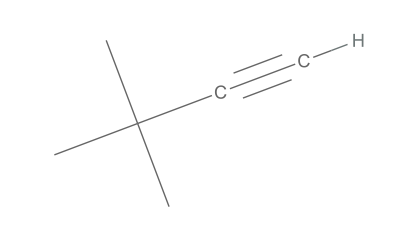
{-Graphics-,-Graphics-}

```mathematica
MoleculePlot[Molecule@#]&/@Normal[Values@combDat[Select[#"true rclass"=="elimination"&]][All,{"true prod","pred prod"}]][[10]]
```

#### Grignard - 50%

```mathematica
grigPMatches=predProdMatches[combDat,"grignard"]
```

{False,False,True,True,False,True,False,True,True,False}

```mathematica
(* 5/10 correct -> 50% raw accuracy on 1st attempt *)
```

```mathematica
N[Counts[grigPMatches][True]/Length[grigPMatches]]*100
```

50.

```mathematica
MoleculePlot[Molecule@#]&/@Normal[Values@combDat[Select[#"true rclass"=="grignard"&]][All,{"true prod","pred prod"}]][[10]];
```